# Physics 234 PS#12 (B) Practice with RNGs

Ziyang Gao
5/6/2018

## Section 1 : What is the problem about

This problem deals with three random number generators : Mathematica' s RandomReal[], the Lehmer Minimal Standard (a = 16807 and m = 231 − 1 = 2147483647), and a Lehmer Sub Standard (a = 78 and m = 127).

## Section 2: Statistical functions

```mathematica
ave[myList_]:=Total[myList]/Length[myList]//N;
aveSqr[myList_]:=Total[myList^2]/Length[myList]//N;
var[myList_]:=aveSqr[myList]-ave[myList]^2;
unc[myList_]:=Sqrt[var[myList]/Length[myList]];
```

## Section 3 : A module that implements the Lehmer Minimal Standard

The code below generates a list of 20 (as an example) random integers implementing the Lehmer Minimal Standard.

```mathematica
z=1;
```

```mathematica
LMS[a_,m_]:=
Module[{},
z=Mod[a*z,m]
]
```

The code below conducts the test suggested at the bottom of the first column on page 1195 in the Park and Mille article, which shows that our implementation is correct:

```mathematica
z=1;
For[i=1,i≤10000,i++,
u= LMS[16807,2147483647];
]
Print["The current value of seed is ",u]
```

The current value of seed is 1043618065

## Section 4 : A time comparison between LMS and Mathematica' s RandomReal[]

The chunk compares the running time of LMS and Mathematica’s random number generator RandomReal[ ].

```mathematica
Timing[LMS[16807,2147483647];RandomReal[]]
```

{0.00063,0.29631}

```mathematica
0.000027/0.420664//N
```

0.0000641842

The result suggests that LMS takes about .000064 the time of RandomReal[ ] takes to generate a random number.

## Section 5 : A module that generates a Lehmer Sub Standard RNG

The chunk implements a module for a Lehmer Sub Standard RNG as defined above. We want to show that the period of this RNG is 126 by (1) cycling through the sequence 400 times and (2) by doing a 1 D Random Walk with 400 steps. In both cases we include data and plots. Besides the short period, what else do you notice from the graph of your 1 D walk that' s bad about this RNG?

The code below cycles LSS sequence 400 times and plots each point. We also checked that at position 3, 129, 255, 381 we get the same number 0.629, which indicates that the period of this RNG is 126. And we can also see from the random number plot that there’s some repetitive pattern reflecting cycles.

{0.629921,0.629921,0.629921,0.629921}

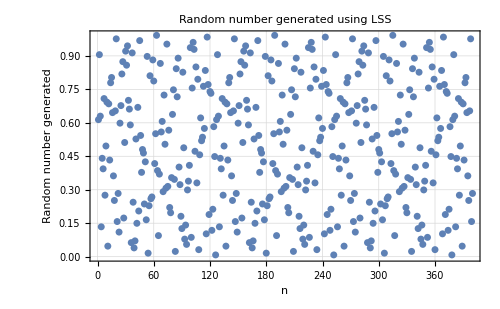

0.133858

```mathematica
z=1;
randList1={};
randList2={};
For[i=1,i≤400,i++,
u= LMS[78,127]/127;
AppendTo[randList1,u//N];
AppendTo[randList2,{i,u//N}];
]
{randList1[[3]],randList1[[129]],randList1[[255]],randList1[[381]]}
plot1=ListPlot[randList2,PlotStyle ->{Blue[1,0,0],PointSize[0.01]},Frame -> True, FrameLabel-> {"n","Random number generated"},PlotRange->All,PlotLabel->Style["Random number generated using LSS",FontFamily->"Helvetica",FontSize->12,FontWeight->"Bold"],GridLines->Automatic,ImageSize->500];
Show[plot1]
randList1[[4]]
```

The following code generates the walking pattern by doing a 1 D Random Walk with 400 steps using randList1. If we get a value < 0.5, move left by one step; otherwise, move right by one step. From the graph we got below, there is an obvious periodic pattern that repeats around step 126.

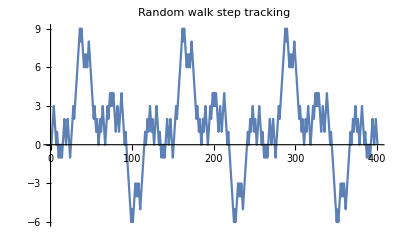

```mathematica
steps[p_]:=If[p<0.5,-1,1];
stepsTrac ={};
For[i=1,i≤400,i++,
AppendTo[stepsTrac,steps[randList1[[i]]]];
]
xValues=FoldList[Plus,0,stepsTrac];
ListLinePlot[xValues,PlotLabel->Style["Random walk step tracking",FontSize->12]]
```

## Section 6 : A module that determines the chi - square value χ2 for a data set

The chunk below will determine χ2 for three data sets. Our module operates on binned data, i.e., a list containing the number of times your data values fall within bins of a certain size. It then generates data consisting of 10, 000 random numbers between 0 and 1 for the three RNGs discussed above. With m = 100 bins, we find the chi - square value for each of the data sets and determine if the RMG passes the χ2 test according to CSM.

```mathematica
listLMS={};
For[i=1,i≤10000,i++,
f=LMS[16807,2147483647]/2147483647;
AppendTo[listLMS,f//N];
]
b1=BinCounts[listLMS,{0,1,0.01}];
ChiSqrLMS=Total[Power[b1-100,2]/100] //N
{1-2/Sqrt[100]//N,ChiSqrLMS/100,1+2/Sqrt[100]//N}
```

112.66

{0.8,1.1266,1.2}

The Lehmer Minimal Standard (LMS) RNG passed the χ2 test.

```mathematica
listLSS={};
For[i=1,i≤10000,i++,
f=LMS[78,127]/127;
AppendTo[listLSS,f//N];
]
b2=BinCounts[listLSS,{0,1,0.01}];
ChiSqrLSS=Total[Power[b2-100,2]/100] //N
{1-2/Sqrt[100]//N,ChiSqrLSS/100,1+2/Sqrt[100]//N}
```

1212.24

{0.8,12.1224,1.2}

The Lehmer Sub Standard (LSS) RNG didn’t pass the χ2 test.

```mathematica
listRandomReal={};
For[i=1,i≤10000,i++,
f=RandomReal[];
AppendTo[listRandomReal,f];
]
b3=BinCounts[listRandomReal,{0,1,0.01}];
ChiSqrRR=Total[Power[b3-100,2]/100] //N
{1-2/Sqrt[100]//N,ChiSqrRR/100,1+2/Sqrt[100]//N}
```

90.24

{0.8,0.9024,1.2}

The Mathematica’s RandomReal[ ] RNG passed the χ2 test.